```mathematica
(* IMPORT MODULES *)
SetDirectory[NotebookDirectory[]];
NotebookEvaluate["modules/oscillator_bracket.nb"];
NotebookEvaluate["modules/operators.nb"];
NotebookEvaluate["modules/mews_and_alphas.nb"];
On[Assert]

(* INITIALIZING PARAMETERS *)
uq=0.315 (* up quark mass *);
sq=0.577 (* strange quark mass *);
cq=1.836(* charm quark mass *);
bq=5.227 (* bottom quark mass *);
sigma=0.1653; (* coefficient of string strength term *)
alphaCoulomb=0.5069; (* coefficient of Coulomb term (0.0175) if you want to replicate Roberts *)
Cqqq=-0.8321(* V = -Subscript[α, C]/r + σr + Subscript[C, qqq] *);
κp=1.8609(* Thing in the spin term *);
CF=1/2(* Colour Factor *);

(* THIS FUNCTION RETURNS THE BARYON HAMILTONIAN FOR A GIVEN ω *)
ClearAll[Hb]
Hb[J_,P_,Isospin_,Λ_,γMax_,ω_,m1_,m2_,m3_,project_]:=Hb[J,P,Isospin,Λ,γMax,ω,m1,m2,m3,project]=Module[
{ projector,sM,vCoulomb,vLinear,spinPart12,spinPart23,spinPart31,v12baryon,v23baryon,v31baryon,kin,mas1,mas2,mas3,cqqq,kinetic,Hbaryon},

projector=Projector[J,P,Λ,γMax,Isospin];

sM=stateMatrix[J,P,Λ,γMax];

vCoulomb=polynomialOperatorRho[sM,-1];
vLinear=polynomialOperatorRho[sM,1];

spinPart12=(8 Pi)/(3m1 m2 r0[m1,m2]^3 Pi^(3/2))κp*GaussOperator[sM,ω,3,m1,m2,m3];
spinPart23=(8 Pi)/(3m2 m3 r0[m2,m3]^3 Pi^(3/2))κp*Transpose[t1].GaussOperator[sM,ω,1,m1,m2,m3].t1;
spinPart31=(8 Pi)/(3m3 m1 r0[m3,m1]^3 Pi^(3/2))κp*Transpose[t2].GaussOperator[sM,ω,2,m1,m2,m3].t2;

v12baryon=-alphaCoulomb*α[m1,m2,ω]*vCoulomb+(sigma*vLinear)/α[m1,m2,ω]+spinPart12;
v23baryon=-alphaCoulomb*α1[m1,m2,m3,ω]*(Transpose[t1].vCoulomb.t1)+(sigma*(Transpose[t1].vLinear.t1))/α1[m1,m2,m3,ω]+spinPart23;
v31baryon=-alphaCoulomb*α2[m1,m2,m3,ω]*(Transpose[t2].vCoulomb.t2)+(sigma*(Transpose[t2].vLinear.t2))/α2[m1,m2,m3,ω]+spinPart31;

kin=kMatrix[sM,ω,m1,m2,m3];
mas1=IdentityMatrix[size]*m1;
mas2=IdentityMatrix[size]*m2;
mas3=IdentityMatrix[size]*m3;
cqqq=IdentityMatrix[size]*(Cqqq);
kinetic=mas1+mas2+mas3+kin;
Hbaryon=kinetic+CF(v12baryon+v23baryon+v31baryon+3*cqqq);
If[project,Hbaryon=ApplyProjector[Hbaryon,projector]];
Return[Hbaryon]
]
```

```mathematica
(* INITIALISE HYPERPARAMETERS AND OBTAIN LOWEST LYING STATE *)

(**** !!!TUNABLE PARAMETERS!!! ****)
(**** !!!TUNABLE PARAMETERS!!! ****)
J=1/2;(* Total angular momentum J = Λ + S *)
P=+1;(* Parity P=(-1)^(Subscript[l, ρ]+Subscript[l, λ]) *)
Isospin=1;(* Isospin *)
γMax=10;(* Maximum energy of considered basis states (2n+l+2N+L), use this to control Subscript[N, Q] *)
Λ=0;(* Total orbital angular momentum Λ = Subscript[l, ρ] + Subscript[l, λ] *)
m1=bq;(* mass of quark 1 *)
m2=bq;(* mass of quark 2 *)
m3=uq;(* mass of quark 3 *)
rangeMin=0.43;(* Minimum of ω range rangeMin≤ω≤rangeMax *)
rangeMax=0.52; (* max of ω range*)
increment=0.01;(* step size (increment size) *)
save=False;(* Do you want to save the {Subscript[ω, i],Subscript[E, i]} for rangeMin≤ω≤rangeMax data to: 'lines/Silvestre/eigenValues/Subscript[q, 1] Subscript[q, 2] Subscript[q, 3]/E{γMax}.mx'? *)
(* Example path: 'lines/Silvestre/eigenValues/uub/E8.mx' *)
(**** !!!END OF TUNABLE PARAMETERS!!! ****)
(**** !!!END OF TUNABLE PARAMETERS!!! ****)
(* Save path parameters *)
If[save,
dirPath=FileNameJoin[{NotebookDirectory[],"lines/Silvestre/eigenValues"}];
quarkDict=Association[{uq->"u",sq->"s",cq->"c",bq->"b"}];
filename=quarkDict[m1]<>quarkDict[m2]<>quarkDict[m3]<>"/"<>"E"<>ToString[γMax]<>".mx"
]

(* Define Subscript[r, 0] parameter, see Silvestre's 1996 paper. Potential: AL1 *)
r0[mi_,mj_]:=1.6553((2mi mj)/(mi+mj))^-0.2204(* Gaussian function parameter *);

(* Choose to project depending if m1=m2 or m1≠m2, True and False, respectively *)
If[m1==m2,project=True,project=False];

(* Obtain projector matrix *)
projector=Projector[J,P,Λ,γMax,Isospin];

(* Calculate generalised transformation matrices *)
t1=tMatrix[J,P,Λ,γMax,m1,m2,m3,1];
t2=tMatrix[J,P,Λ,γMax,m1,m2,m3,2];

(* Obtain size of basis from size of talmi matrices (Subscript[N, Q]) *)
size=Dimensions[t1][[1]];

(* If projector has been applied, find position of first non-zero eigenvalue, if not applied then it's 1 *)
If[project==True,firstNonZero=size-Total[Diagonal[projector]]+1,firstNonZero=1];
```

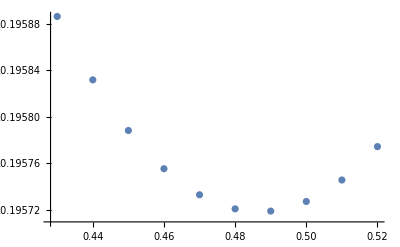

{14.341,14.3324,14.2747,14.2334,14.2135,14.2087,14.1218,14.1102,14.1046,14.0629,14.0172,14.0122,13.9734,13.944,13.8712,13.7616,13.737,13.7026,13.6623,13.6082,13.5605,13.0721,13.0392,13.0284,12.9323,12.8939,12.8893,12.8615,12.7727,12.749,12.7261,12.7144,12.6737,12.6525,12.6188,12.5716,12.1425,12.1045,12.1012,12.029,11.97,11.9665,11.9545,11.8462,11.8202,11.6532,11.4839,11.4684,11.4365,11.2916,11.2558,11.0057,10.8969,10.8761,10.5552,10.196,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Successfully Found Minimum

{0.49,10.1957}

```mathematica
(* Obtain a table of {{ω,E}} sets for varying ω to determine lowest Eigenvalue *)
tab=Table[{ω,Eigenvalues[Hb[J,P,Isospin,Λ,γMax,ω,m1,m2,m3,project]][[-firstNonZero]]-(2.02*10^-3)/(m1*m2*m3)},{ω,rangeMin,rangeMax,increment}];

(* Plot the list of above set of {{ω,E}} (The U-plot) *)
ListPlot[tab]

(* Extract ω's and Eigenvalues separately *)
omegas=tab[[All,1]];
evals=tab[[All,2]];
(* Find value of minimum eigenvalue *)
minEval=Min[evals];
(* Find positional index of minimum eigenvalue *)
posOfMinEval=Position[evals,minEval][[1,1]];
(* Use positional index of minimum eigenvalue to obtain the corresponding value of ω *)
optimumOmega=omegas[[posOfMinEval]];
(* Construct a list object containing {Subscript[ω, min],Subscript[E, min]} *)
minimum={optimumOmega,minEval};

(* Print all eigenvalues for all ω's *)
Print[Eigenvalues[Hb[J,P,Isospin,Λ,γMax,optimumOmega,m1,m2,m3,project]]//Chop]

(* Initiate an error counter, will go up by one for each error encountered *)
errors=0;
(* First, check if the list object {Subscript[ω, min],Subscript[E, min]} exists in the list of all {{ω,E}} *)
If[tab[[posOfMinEval]]!=minimum,errors+=1;Print["Does not agree"]]
(* Check if Subscript[E, min] is the first element of {{ω,E}}, if True, extend ω range to the left *)
If[posOfMinEval==1,errors+=1;Print["Need to extend range more to the left"]]
(* Check if Subscript[E, min] is the last element of {{ω,E}}, if True, extend ω range to the right *)
If[posOfMinEval==Length[tab],errors+=1;Print["Need to extend range more to the right"]]
(* Finally if no errors encountered print {Subscript[ω, min],Subscript[E, min]} *)
If[errors==0,Print["Successfully Found Minimum"];Print[minimum];]

(* Save data *)
If[save==True,
fullPath=FileNameJoin[{dirPath,filename}];
Print["Successfully saved to:"];
Export[fullPath,tab]]
```

{0.4,0.5,0.6,0.7,0.8}

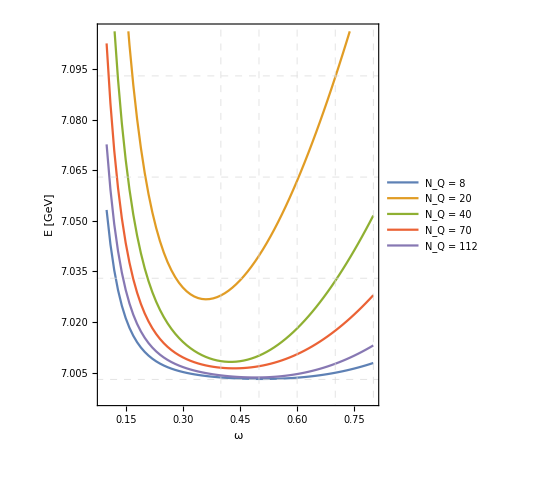

```mathematica
(* PLOTTING MASS PLOTS *)
allLinePaths=FileNames[All,"lines/Silvestre/eigenValues/scb"];
allFilenames=Table[FileNameJoin[{NotebookDirectory[],allLinePaths[[i]]}],{i,1,Length[allLinePaths]}];
allLinesData=Table[Import[allFilenames[[i]]],{i,1,Length[allFilenames]}];

plotRange={{0.09,0.8},Automatic};
frameTicks={{Automatic,None}, {Automatic,None}};
legendFontSize=14;
labelFontSize=14;
fontFamily="Times";
plotLegends={Placed[{Style["N_Q = 8",FontSize->legendFontSize,FontFamily->fontFamily],
Style["N_Q = 20",FontSize->legendFontSize,FontFamily->fontFamily],Style["N_Q = 40",FontSize->legendFontSize,FontFamily->fontFamily],
Style["N_Q = 70",FontSize->legendFontSize,FontFamily->fontFamily],
Style["N_Q = 112",FontSize->legendFontSize,FontFamily->fontFamily]
},{Center,Top}]};
labelStyle={FontSize->labelFontSize, FontFamily->fontFamily,Black};
frameLabel={{"E [GeV]",None},{"ω","Ω_cb, (scb)"}};
frame={{True,True},{True,True}};
vertGridLines=Table[7.003+x,{x,0,0.1,0.03}];
horzGridLines=Table[x,{x,0.4,0.8,0.1}]
gridLines={horzGridLines,vertGridLines};
gridLinesStyle=Directive[Dashed, LightGray];

plot=ListPlot[allLinesData,Joined->True,PlotRange->plotRange,
FrameTicks->frameTicks,
PlotLegends->plotLegends,
LabelStyle->labelStyle,
FrameLabel->frameLabel,
Frame->frame,
AspectRatio->1.2,
GridLines->gridLines,
GridLinesStyle->gridLinesStyle]
```

```mathematica
Export["plots/baryons/eigVals/scbEvsW.pdf",plot,"PDF","AllowRasterization"->False]
```

plots/baryons/eigVals/scbEvsW.pdf

```mathematica
Length[h[1]]
```

1

```mathematica
(* Get state matrix *)
sM=stateMatrix[J,P,Λ,γMax];
(* Obtain observable in 12 frame *)
observable12=delta3RhoMatrix[sM];
(* transform the observable in to frame 23 *)
observable23=Transpose[t1].delta3RhoMatrix[sM].t1;
(* transform the observable in to frame 31 *)
observable31=Transpose[t2].observable12.t2;
(* Collect observables into a list that we can iterate over *)
observables={observable12,observable23,observable31};
alphas={α[m1,m2,wMin],α1[m1,m2,m3,wMin],α2[m1,m2,m3,wMin]};
eVec[omega_]:=(
ω=omega;
evec=Eigenvectors[Hb[J,P,Isospin,Λ,γMax,omega,m1,m2,m3,project]-IdentityMatrix[Length[sM]]*(2.02*10^-3)/(m1*m2*m3)][[-firstNonZero]]//Chop
)
expVals=Table[α[m1,m2,wMin]^3*eVec[wMin].observables[[i]].eVec[wMin]*1800.149,{i,1,3}];
Print["Expectation Value at ω_min: ",expVals]
Print["ω_min: ",wMin]
```

Expectation Value at ω_min: {22.7766,14.6119,14.6119}

ω_min: 0.52

```mathematica
?α2
```

{0.,-2.33928,0.,0.560751,0.106239,0.,0.,0.303791,0.,-0.240946,0.0016466,0.,0.,-0.111195,0.,-0.19898,0.00280398,0.,0.,-0.106032,0.,0.0768851,0.00677868,0.,0.,-0.00692993,0.0119665,0.,0.,0.0425701,0.0130784,0.,0.,-0.00109014,0.,0.0329691,0.00607814,0.,0.,0.0228662,0.,-0.0301249,0.000334949,0.,0.,-0.0129351,0.00353858,0.,0.,-0.015414,0.,-0.0274225,0.00351259,0.,0.,-0.0223389,0.00178249,0.,0.,-0.0273068,0.00185058,0.,0.,-0.0071179,0.,-0.0156817,0.00186192,0.,0.,-0.00772181}

{0,-0.953024,0,0.228451,0.0432818,0,0,0.123765,0,-0.0981616,0.000670825,0,0,-0.045301,0,-0.0810646,0.00114234,0,0,-0.0431978,0,0.0313231,0.00276164,0,0,-0.00282326,0.00487515,0,0,0.0173431,0.00532814,0,0,-0.000444125,0,0.0134316,0.00247624,0,0,0.00931573,0,-0.0122729,0.000136458,0,0,-0.00526979,0.00144162,0,0,-0.00627967,0,-0.0111719,0.00143103,0,0,-0.00910088,0.000726189,0,0,-0.0111248,0.000753927,0,0,-0.00289984,0,-0.00638872,0.000758548,0,0,-0.00314587}

2.45458

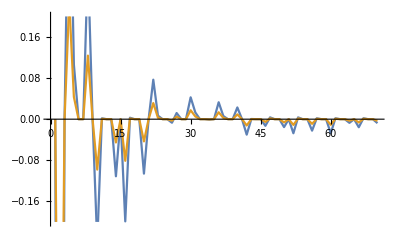

```mathematica
pos=36;
h=Hb[J,P,Isospin,Λ,γMax,minimum[[1]],m1,m2,m3,project]-IdentityMatrix[Length[sM]]*(2.02*10^-3)/(m1*m2*m3);
vec[pos_]:=Eigenvectors[h][[-pos]]//Chop
Hpsi=h.vec[pos]
Epsi=vec[pos]
Hpsi[[2]]/Epsi[[2]]
ListPlot[{Hpsi,Epsi},Joined->True,PlotRange->{-0.2,0.2}]
```